Digital Humanities 1011 - In class assignment 8
Name : Dustin Dobransky
Id : 250575030
Email : ddobran@uwo.ca
Date : 2016 - 01 - 10

Description: Uses the table command to draw a picture.  I originally tried to write a recursive function to generate the fractals below to some n-levels deep, but couldn’t get the mathematica syntax to cooperate.

8

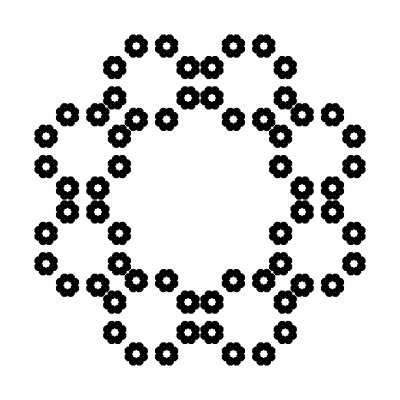

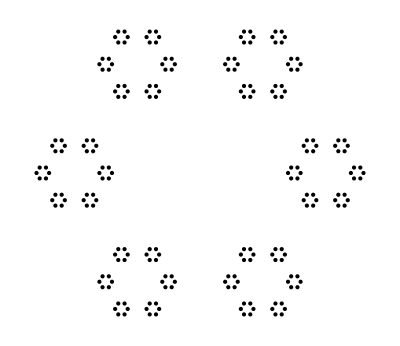

```mathematica
nPoints = 8

createCirclyCoords[{point_, scale_}] := Table[point + x*scale,{x,CirclePoints[nPoints]}]

Graphics[
Point[
FlattenAt[
Table[createCirclyCoords[{z,.015}], {z, 
FlattenAt[
Table[createCirclyCoords[{y,.05}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[nPoints]*.8}],
Table[{a},{a, 1, nPoints^1, 1}]
]
}],
Table[{b},{b,1,nPoints^2,1}]
]}
],
Table[{c},{c,1,nPoints^3,1}]
]
],
ImageSize->Full
]

nPoints = 6;

Graphics[
Point[
FlattenAt[
Table[createCirclyCoords[{y,.05}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[nPoints]}],
Table[{a},{a, 1, nPoints, 1}]
]
}],
Table[{b},{b,1,nPoints^2,1}]
]
]
]
```